```mathematica
Remove["Global`*"]
```

```mathematica
E[x_,y_] = 1/((x-1/2)^2+y^2) +1/((x+1/2)^2+y^2) -2/(x^2+(y-3^(1/2)/2)^2)
```

1/((-1/2+x)^2+y^2)+1/((1/2+x)^2+y^2)-2/(x^2+(-(√3)/2+y)^2)

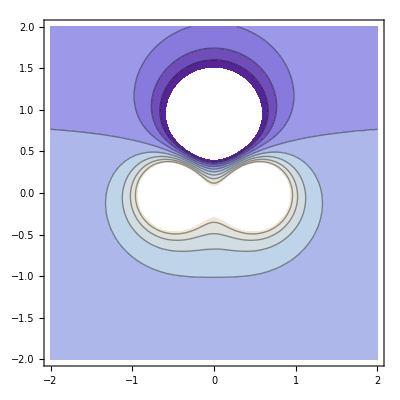

```mathematica
ContourPlot[E[x,y],{x,-2,2},{y,-2,2}]
```

```mathematica
Integrate[E[x,y],{x,y}]
```

```mathematica
Remove["Global`*"]
```

```mathematica
ThSoln = DSolve[{D[ϕ[t,x],t,t]-D[ϕ[t,x],x,x]==m^2*ϕ[t,x]-λ*ϕ[t,x]^3},ϕ,{x,t}]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{ϕ→Function[{t,x},-(m Tanh[x C[2]-(t √(-m^2+2 C[2]^2))/(√2)+C[3]])/(√λ)]},{ϕ→Function[{t,x},(m Tanh[x C[2]-(t √(-m^2+2 C[2]^2))/(√2)+C[3]])/(√λ)]},{ϕ→Function[{t,x},-(m Tanh[x C[2]+(t √(-m^2+2 C[2]^2))/(√2)+C[3]])/(√λ)]},{ϕ→Function[{t,x},(m Tanh[x C[2]+(t √(-m^2+2 C[2]^2))/(√2)+C[3]])/(√λ)]}}

```mathematica
ϕ[t_,x_] = ϕ[t,x]/.ThSoln[[2]]
```

(m Tanh[x C[2]-(t √(-m^2+2 C[2]^2))/(√2)+C[3]])/(√λ)

```mathematica
V=0.0;m=1;λ=0.5;Subscript[x, 0]=0;
ThModel[t_,x_] = ϕ[t,x]/.{C[2]->m/((2*(1-V^2))^(1/2)),C[3]->-Subscript[x, 0]*C[2]}
```

(0.-1.41421 ⅈ) Tan[(1.05367×10^-8+0. ⅈ) t+(0.+0.707107 ⅈ) x]

```mathematica
ThModel[0,x]
```

(0.-1.41421 ⅈ) Tan[(0.+0. ⅈ)+(0.+0.707107 ⅈ) x]

```mathematica
ThModel[1,x]
```

(0.-1.41421 ⅈ) Tan[(1.05367×10^-8+0. ⅈ)+(0.+0.707107 ⅈ) x]

```mathematica
ThModel[t,0]
```

(0.-1.41421 ⅈ) Tan[(0.+0. ⅈ)+(1.05367×10^-8+0. ⅈ) t]

```mathematica
ThModel[t,1]
```

(1.41421+0. ⅈ) Tanh[(0.707107+0. ⅈ)-(0.+1.05367×10^-8 ⅈ) t]

As can be seen, the special solution constructed by mathematica is similar to the solution of the given equation mentioned in the assignment sheet where C[2] = m/(2*(1-v^2))^(1/2) and V = (-m^2+2C[2]^2)^(1/2) and C[3]/C[2] = x0

```mathematica
m = 1;λ=0.5;V=0;Subscript[x, 0]=0;
ϕEqn = D[ϕ[t,x],t,t]-D[ϕ[t,x],x,x]==m^2*ϕ[t,x]-λ*ϕ[t,x]^3
ϕsoln = NDSolve[{ϕEqn,ϕ[t,0]==ThModel[t,0], ϕ[t,1]==ThModel[t,1], ϕ[0,x]==ThModel[0,x]},ϕ,{x,0,1},{t,0,1}]
```

2.82843 C[2]^2 Sech[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]^2 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]-1.41421 (-1+2 C[2]^2) Sech[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]^2 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]==1.41421 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]-1.41421 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]^3

NDSolve::ndode: Input is not an ordinary differential equation.

NDSolve[{2.82843 C[2]^2 Sech[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]^2 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]-1.41421 (-1+2 C[2]^2) Sech[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]^2 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]==1.41421 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]-1.41421 Tanh[x C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]^3,-1.41421 Tanh[(t √(-1+2 C[2]^2))/(√2)-C[3]]==(0.-1.41421 ⅈ) Tan[(0.+0. ⅈ)+(1.05367×10^-8+0. ⅈ) t],1.41421 Tanh[C[2]-(t √(-1+2 C[2]^2))/(√2)+C[3]]==(1.41421+0. ⅈ) Tanh[(0.707107+0. ⅈ)-(0.+1.05367×10^-8 ⅈ) t],1.41421 Tanh[x C[2]+C[3]]==(0.-1.41421 ⅈ) Tan[(0.+0. ⅈ)+(0.+0.707107 ⅈ) x]},ϕ,{x,0,1},{t,0,1}]